# Parametric Sweep - Processing

## Last Updated: 2025/07/19

```mathematica
(*Quit[];*)
```

```mathematica
(*Remove["Global`*"];
ClearInOut[];*)
```

```mathematica
(*note: para phase curves form a closed area*)
```

# General

## Plotting

```mathematica
(*set plot options*)
SetOptions[Plot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Joined->False,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListLinePlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic,GridLines->Automatic];
SetOptions[ListLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];SetOptions[ListLogLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set signal plot options*)
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set 3d plot options*)
SetOptions[ListDensityPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot3D,Background->None,ImageSize->Large];
```

```mathematica
(*get default plot colors*)
DefaultPlotColors=Cases[#,_?ColorQ,All]&["DefaultPlotStyle"/. (Method/. Charting`ResolvePlotTheme[Automatic,Plot])];
```

## Evaluations

```mathematica
(*turn upsetting things off*)
ParallelEvaluate[
Off[General::munfl];
Off[FindRoot::lstol];
Off[FindFit::cvmit];
Off[FindFit::sszero];
Off[FindFit::nrjnum];
Off[NonlinearModelFit::cvmit];
Off[NonlinearModelFit::sszero];
Off[Power::infy];
Off[Infinity::indet];
Off[FittedModel::constr];
];
Evaluate[
Off[General::munfl];
Off[FindRoot::lstol];
Off[FindFit::cvmit];
Off[FindFit::sszero];
Off[FindFit::nrjnum];
Off[NonlinearModelFit::cvmit];
Off[NonlinearModelFit::sszero];
Off[Power::infy];
Off[Infinity::indet];
Off[FittedModel::constr];
];
```

## Dataset Processing

```mathematica
(*import raw counts and demodulate*)
ProcessDatasetCounts[filename_]:=Module[
{
(*actual data*)
dataset,
datasetFrequencies=Import[filename,{"/datasets/xArr"}],
datasetCounts=Import[filename,{"/datasets/results"}],
correlatedSignal,correlatedAmplitude,correlatedPhase,
(*parameters*)
modulationAmplitude=Import[filename,{"/datasets/modulation_amplitude_vpp"}],
shimVoltage=Import[filename,{"/datasets/dc_channel_voltage"}],
(*processing*)
results
},

(*refine dataset*)
dataset=AssociationThread[datasetFrequencies->datasetCounts];
(*dataset=KeySort[dataset];*)

(*demodulate counts*)
correlatedSignal=KeyValueMap[
Total[Exp[ⅈ*(2*π*#1*1*^6)*#2]]/Length[#2]&,
dataset
];
{correlatedAmplitude,correlatedSignal}=Transpose[AbsArg[correlatedSignal]];

(*format data*)
results=Transpose[
{datasetFrequencies,ConstantArray[shimVoltage,Length[correlatedAmplitude]],##}&@@{correlatedAmplitude,correlatedSignal}
];

(*clean up mess*)
Remove[dataset,datasetFrequencies,datasetCounts];
ClearSystemCache[];
ClearInOut[];

(*return dataset*)
Return[results];
];
```

```mathematica
(*import already demodulated dataset*)
ProcessDataset[filename_]:=Module[
{
(*actual data*)
datasetRaw=Import[filename,{"/datasets/results"}],
(*parameters*)
(*modulationAmplitude=Import[filename,{"/datasets/modulation_amplitude_vpp"}],
shimVoltage=Import[filename,{"/datasets/dc_channel_voltage"}],*)
(*processing*)
results
},

(*refine dataset*)
(*dataset=KeySort[dataset];*)

(*format data*)
(*results=Transpose[
(datasetRaw[[;;,1]],ConstantArray[shimVoltage,Length[datasetRaw]],datasetRaw[[;;,3]],datasetRaw[[;;,4]]}
];*)
results=datasetRaw;

(*clean up mess*)
Remove[datasetRaw];
ClearSystemCache[];
ClearInOut[];

(*return dataset*)
Return[results];
];
```

# User Input

```mathematica
(*top level directory for imports*)
directoryString="Z:\\motion\\Data\\2026-08\\2026-08-21";
```

```mathematica
(*select run*)
rid=163077;
```

```mathematica
(*data limit fitting tmp todo*)
tmpParam=10;
sweepNum=4;
```

## Process User Input

```mathematica
(*select file with give RID from all subdirectories*)
filenamesAll=FileNames["*.h5",directoryString,Infinity];
filenamesDJ=Select[filenamesAll,StringContainsQ[#,ToString[rid]]&];
```

```mathematica
(*just select dataset of interest as the first one that shows up that matches our RID*)
filenameDJ=First@filenamesDJ;
```

```mathematica
(*check input directory exists*)
If[!DirectoryQ[directoryString],
MessageDialog["Failure :(\nError: Import directory not found ("<>directoryString<>")."];
FrontEndTokenExecute["EvaluatorAbort"];
];
```

```mathematica
(*check desired file exists*)
If[!FileExistsQ[filenameDJ],
MessageDialog["Failure :(\nError: Specified file not found ("<>filenameDJ<>")."];
FrontEndTokenExecute["EvaluatorAbort"]
];
```

```mathematica
(*check desired file is correct for processing*)
If[!StringContainsQ[filenamesDJ[[1]],"parametric",IgnoreCase->True],
MessageDialog["Failure :(\nError: Selected file incompatible with this Notebook.\nSelected file: "<>filenameDJ<>"."];
FrontEndTokenExecute["EvaluatorAbort"]
];
```

# PROCESSING

## Import

## Extract Main Dataset

```mathematica
(*import and process data*)
dataset=ProcessDataset[filenameDJ];
```

```mathematica
(*(*tmp remove! xum comp process*)
(*get relevant parameters*)
{repetitionsPerVoltage,numSteps}=Lookup[parameterList,{"repetitions_per_voltage","num_steps"}];
(*get start/stop indices for extracting only the relevant sweep of interest*)
startIndex=repetitionsPerVoltage*numSteps*2*(sweepNum-1)+1;
stopIndex=repetitionsPerVoltage*numSteps*2*(sweepNum);
(*slice dataset!*)
dataset//Dimensions
dataset=dataset[[startIndex;;stopIndex]];
dataset//Dimensions
(*tmp remove! xum comp process*)*)
```

```mathematica
(*sort dataset*)
dataset=SortBy[dataset,First];
```

## Extract Parameters

```mathematica
(*extract dict of all relevant parameters*)
parameterList=Import[filenameDJ,{"Attributes","/arguments"}];
```

```mathematica
(*get parameters from .hdf5*)
{
shimChannelName,
modAttenuation,
numCounts,
coolingAmplitude,
coolingFrequency
}=parameterList[#]&/@{
"dc_channel",
"mod_att_db",
"num_counts",
"ampl_cooling_pct",
"freq_cooling_mhz"
};
```

## Process

## General Data Formatting

```mathematica
(*separate data by shim voltage and frequency, and average results for same shim/frequency combination*)
individualPlotData=GroupBy[
dataset,
{#[[2]]&,#[[;;2]]&},
Mean]//KeySort;
(*turn resulting association at each voltage into a list, and sort*)
individualPlotData=Sort/@(Values/@individualPlotData);
```

```mathematica
(*get min/max IV values for plotting later on*)
{indVar1Min,indVar1Max}={Min[#],Max[#]}&[individualPlotData[[1,;;,1]]];
```

```mathematica
(*return only a section of the dataset centered around the max amplitude; helpful for eliminating statistical noise and speeding up fitting*)
ReduceDataset[data_,rangeLimiter_]:=Module[
{
maxInd=First@Ordering[data[[;;,2]],-1],
spanSteps=Round[N[rangeLimiter]/((data[[-1,1]]-data[[1,1]])/Length[data])],
redIndStart,redIndStop
},
{redIndStart,redIndStop}=Clip[#,{1,Length[data]}]&/@{maxInd-spanSteps,maxInd+spanSteps};
Return[data[[redIndStart;;redIndStop]]];
];
```

```mathematica
(*workaround to plot single voltage sweeps*)
If[
Dimensions[Values[individualPlotData]][[2]]==1,
individualPlotData={#[[1]],#[[1]]+{0.1,0.,0.,0.,0.}}&/@individualPlotData;
singleFrequencyFlag=True;,
singleFrequencyFlag=False;
];
```

```mathematica
(*create reduced datasets*)
reducedDataset=ReduceDataset[#[[;;,{1,3,4}]],tmpParam/1000]&/@individualPlotData;
```

## Process Amplitude

```mathematica
(*get and reduce amplitude data*)
amplitudeData=#[[;;,{1,2}]]&/@individualPlotData;
reducedAmplitudeData=#[[;;,{1,2}]]&/@reducedDataset;
```

```mathematica
(*guess amplitude values*)
guessAmplitudeFitParams=Values[#[[First@Ordering[#[[;;,2]],-1]]]&/@reducedAmplitudeData];
(*guess linewidth as ~1 kHz (i.e. 0.001)*)
guessAmplitudeFitParams=Map[
{#2*0.001/2 √(2*#1^2-0.001),#1,0.001}&@@#&,
guessAmplitudeFitParams
];
```

### Fit Amplitude

```mathematica
(*create lorentz model for fitting*)
amplitudeModel=α/(√((x^2-β^2)^2+(x*γ)^2));
amplitudeConstraints={β<4,β>0};
```

```mathematica
(*fit amplitude model - nonlinearmodelfit to extract extra fit information*)
AbsoluteTiming[
amplitudeFitsFull=ParallelMap[
NonlinearModelFit[
reducedAmplitudeData[[#]],
Join[{amplitudeModel,amplitudeConstraints}],
Transpose[{{α,β,γ},guessAmplitudeFitParams[[#]]}],
x
]&,
Range[Length[reducedAmplitudeData]]
];
]
amplitudeFitsFull=AssociationThread[Keys[reducedAmplitudeData]->amplitudeFitsFull];
```

{0.131077,Null}

### Process Fitted Amplitude Results

```mathematica
(*extract relevant data*)
amplitudeFits=(#["BestFitParameters"])&/@amplitudeFitsFull;
amplitudeFunctions=(#["BestFit"])&/@amplitudeFitsFull;
amplitudeFitConfidenceValues=(#["ParameterConfidenceIntervalTableEntries"])&/@amplitudeFitsFull;
```

FittedModel::dof: The number of parameters 3 is not less than the number of data values 1. Some property values cannot be computed.

FittedModel::varzero: The estimated variance is zero. Properties requiring division by the variance or standard error will not be computed.

FittedModel::dof: The number of parameters 3 is not less than the number of data values 1. Some property values cannot be computed.

FittedModel::varzero: The estimated variance is zero. Properties requiring division by the variance or standard error will not be computed.

FittedModel::dof: The number of parameters 3 is not less than the number of data values 1. Some property values cannot be computed.

General::stop: Further output of FittedModel::dof will be suppressed during this calculation.

FittedModel::varzero: The estimated variance is zero. Properties requiring division by the variance or standard error will not be computed.

General::stop: Further output of FittedModel::varzero will be suppressed during this calculation.

```mathematica
(*create fitted amplitude plots*)
fittedAmplitudePlots=Plot[
Callout[
amplitudeFunctions[#],
amplitudeFitConfidenceValues[#][[2,1]]*1000.,
Above,
LabelStyle->Directive[13],
CalloutMarker->"Circle"
],
{x,indVar1Min,indVar1Max},
PlotStyle->{{Dashed,Orange}},
PlotRange->Full
]&/@Keys[amplitudeFunctions];
fittedAmplitudePlots=AssociationThread[Keys[reducedAmplitudeData]->fittedAmplitudePlots];
```

Plot::plld: Endpoints for x in {x,1.511,1.511} must have distinct machine-precision numerical values.

General::stop: Further output of Plot::plld will be suppressed during this calculation.

### Plot Individual Amplitudes

```mathematica
(*amplitude plots*)
amplitudePlots=ListLinePlot[
{
#[[;;,{1,3}]],
#[[;;,{1,3}]]
(*{Callout[{0.766,0.05},Below]}*)
},
PlotRange->Full,
FrameLabel->{ 
{Style["Correlated Fraction",{Black,Directive[15]}],None},
{Style["Frequency (MHz)",{Black,Directive[15]}],Style["Correlated Signal Amplitude - RID: "<>ToString[rid]<>"\n"<>shimChannelName<>" = "<>ToString[#[[1,2]]]<>" V",{Black,Directive[15]}]}
},
PlotStyle->{{Automatic,PointSize[0.01],Opacity[0.8]},{Dashed,Blue,Opacity[0.4]}},
Joined->{False,True},
ImageSize->Scaled[0.3]
]&/@individualPlotData;
```

```mathematica
(*plot raw data with fit line*)
amplitudeFinalPlots=MapThread[
Show[#1,#2]&,
Transpose[{amplitudePlots,fittedAmplitudePlots}]
];
```

Show::gcomb: Could not combine the graphics objects in Show[,Plot[Callout[amplitudeFunctions[50.],amplitudeFitConfidenceValues[50.]⟦2,1⟧ 1000.,Above,LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{{Dashed,Orange}},PlotRange→Full]].

Show::gcomb: Could not combine the graphics objects in Show[,Plot[Callout[amplitudeFunctions[50.5],amplitudeFitConfidenceValues[50.5]⟦2,1⟧ 1000.,Above,LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{{Dashed,Orange}},PlotRange→Full]].

Show::gcomb: Could not combine the graphics objects in Show[,Plot[Callout[amplitudeFunctions[51.],amplitudeFitConfidenceValues[51.]⟦2,1⟧ 1000.,Above,LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{{Dashed,Orange}},PlotRange→Full]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

### Extract Resonances

```mathematica
(*extract amplitude resonances*)
fittedAmplitudeResPlotData=Transpose[{Values[#],Keys[#]}&[β/.#&/@amplitudeFits]];
```

```mathematica
(*plot resonances*)
amplitudeResPlot=ListPlot[
fittedAmplitudeResPlotData,
Joined->False,
PlotStyle->{Red,Dashed},
PlotRange->Automatic
];
```

## Process Phase

```mathematica
(*get and reduce phase data*)
phaseData=#[[;;,{1,4}]]&/@individualPlotData;
reducedPhaseData=#[[;;,{1,3}]]&/@reducedDataset;
```

```mathematica
(*guess phase values*)
guessPhaseFitα=π/2;
guessPhaseFitβ=Median[fittedAmplitudeResPlotData[[;;,1]]];
guessPhaseFitγ=0.0005;
guessPhaseFitδ=FindThreshold[#[[;;,2]]]&/@reducedPhaseData;
```

### Rotate Phase (Phase Unwrapping)

```mathematica
PhaseRotate[dataset_,angle_]:=Module[
{
phaseX=dataset[[;;,1]],
phaseValues=dataset[[;;,2]],
rotatedPhaseValues
},

(*rotatedPhaseValues=Arg[Exp[ⅈ*dataset[[;;,2]]]*Exp[ⅈ*angle]];*)
rotatedPhaseValues=Arg[Exp[ⅈ*(dataset[[;;,2]]-angle)]];

Return[Transpose[{phaseX,rotatedPhaseValues}]]
];
```

```mathematica
PhaseThreshold[dataset_]:=Module[
{
phaseValues=dataset[[;;,2]],
phaseThreshold1,
phaseMean1,
phaseValues2,
phaseMean2,
phaseThreshold2
},

(*cycle 1*)
phaseThreshold1=FindThreshold[Arg[Exp[ⅈ*phaseValues]]];
phaseMean1=GroupBy[phaseValues,#>phaseThreshold1&,Mean];
phaseMean1=Mean[Values[phaseMean1]];

(*cycle 2*)
phaseValues2=Arg[Exp[ⅈ*(phaseValues-phaseMean1)]];
phaseThreshold2=FindThreshold[phaseValues2];
phaseMean2=GroupBy[phaseValues2,#>phaseThreshold2&,Mean];
phaseMean2=Mean[Values[phaseMean2]];

(*return sum of phases*)
Return[phaseMean1+phaseMean2]
];
```

```mathematica
(*shift phase to compensate for limited range of arg[z]/arctan[z]*)
(*shiftedReducedPhaseData=PhaseRotate[#,PhaseThreshold[#]]&/@reducedPhaseData;*)
shiftedReducedPhaseData=reducedPhaseData;
```

### Fit Phases

```mathematica
(*create phase model*)
phaseModel=α*Erf[(x-β)/γ]+δ;
phaseConstraints={(*α<2*π,β>0,γ<π,γ>0*)};
```

```mathematica
(*fit phase model - nonlinearmodelfit to extract extra fit information*)
AbsoluteTiming[
phaseFitsFull=ParallelMap[
NonlinearModelFit[
shiftedReducedPhaseData[[#]],
Join[{phaseModel,phaseConstraints}],
{{α,π/2},{β,guessPhaseFitβ},{γ,0.0005},{δ,guessPhaseFitδ[[#]]}},
x
]&,
Range[Length[shiftedReducedPhaseData]]
];
]
phaseFitsFull=AssociationThread[Keys[shiftedReducedPhaseData]->phaseFitsFull];
```

{0.0367229,Null}

```mathematica
(*phaseFitConfidenceValues[[;;,1,1]]//Values;
{Median[%],Mean[%],Histogram[%],FindThreshold[%]}
phaseFitConfidenceValues[[;;,2,1]]//Values;
{Median[%],Mean[%],Histogram[%],FindThreshold[%]}
phaseFitConfidenceValues[[;;,3,1]]//Values;
{Median[%],Mean[%],Histogram[%],FindThreshold[%]}
phaseFitConfidenceValues[[;;,4,1]]//Values;
{Median[%],Mean[%],Histogram[%],FindThreshold[%]}*)
```

### Process Fitted Phase Results

```mathematica
(*extract relevant data*)
phaseFits=(#["BestFitParameters"])&/@phaseFitsFull;
phaseFunctions=(#["BestFit"])&/@phaseFitsFull;
phaseFitConfidenceValues=(#["ParameterConfidenceIntervalTableEntries"])&/@phaseFitsFull;
```

FittedModel::dof: The number of parameters 4 is not less than the number of data values 1. Some property values cannot be computed.

FittedModel::varzero: The estimated variance is zero. Properties requiring division by the variance or standard error will not be computed.

FittedModel::dof: The number of parameters 4 is not less than the number of data values 1. Some property values cannot be computed.

FittedModel::varzero: The estimated variance is zero. Properties requiring division by the variance or standard error will not be computed.

FittedModel::dof: The number of parameters 4 is not less than the number of data values 1. Some property values cannot be computed.

General::stop: Further output of FittedModel::dof will be suppressed during this calculation.

FittedModel::varzero: The estimated variance is zero. Properties requiring division by the variance or standard error will not be computed.

General::stop: Further output of FittedModel::varzero will be suppressed during this calculation.

```mathematica
(*create fitted plots for visualization*)
fittedPhasePlots=Plot[
Callout[
phaseFunctions[#],
phaseFitConfidenceValues[#][[2,1]]*1000.,
Scaled[0.5],
LabelStyle->Directive[13],
CalloutMarker->"Circle"
],
{x,indVar1Min,indVar1Max},
PlotStyle->{Dashed,Orange}
]&/@Keys[phaseFunctions];
fittedPhasePlots=AssociationThread[Keys[phaseData]->fittedPhasePlots]
```

Plot::plld: Endpoints for x in {x,1.511,1.511} must have distinct machine-precision numerical values.

General::stop: Further output of Plot::plld will be suppressed during this calculation.

<|50.→Plot[Callout[phaseFunctions[50.],phaseFitConfidenceValues[50.]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],50.5→Plot[Callout[phaseFunctions[50.5],phaseFitConfidenceValues[50.5]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],51.→Plot[Callout[phaseFunctions[51.],phaseFitConfidenceValues[51.]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],51.5→Plot[Callout[phaseFunctions[51.5],phaseFitConfidenceValues[51.5]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],52.→Plot[Callout[phaseFunctions[52.],phaseFitConfidenceValues[52.]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],52.5→Plot[Callout[phaseFunctions[52.5],phaseFitConfidenceValues[52.5]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],53.→Plot[Callout[phaseFunctions[53.],phaseFitConfidenceValues[53.]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],53.5→Plot[Callout[phaseFunctions[53.5],phaseFitConfidenceValues[53.5]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],54.→Plot[Callout[phaseFunctions[54.],phaseFitConfidenceValues[54.]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],54.5→Plot[Callout[phaseFunctions[54.5],phaseFitConfidenceValues[54.5]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],55.→Plot[Callout[phaseFunctions[55.],phaseFitConfidenceValues[55.]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],55.5→Plot[Callout[phaseFunctions[55.5],phaseFitConfidenceValues[55.5]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],56.→Plot[Callout[phaseFunctions[56.],phaseFitConfidenceValues[56.]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],56.5→Plot[Callout[phaseFunctions[56.5],phaseFitConfidenceValues[56.5]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],57.→Plot[Callout[phaseFunctions[57.],phaseFitConfidenceValues[57.]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],57.5→Plot[Callout[phaseFunctions[57.5],phaseFitConfidenceValues[57.5]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],58.→Plot[Callout[phaseFunctions[58.],phaseFitConfidenceValues[58.]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],58.5→Plot[Callout[phaseFunctions[58.5],phaseFitConfidenceValues[58.5]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],59.→Plot[Callout[phaseFunctions[59.],phaseFitConfidenceValues[59.]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],59.5→Plot[Callout[phaseFunctions[59.5],phaseFitConfidenceValues[59.5]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],60.→Plot[Callout[phaseFunctions[60.],phaseFitConfidenceValues[60.]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],60.5→Plot[Callout[phaseFunctions[60.5],phaseFitConfidenceValues[60.5]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],61.→Plot[Callout[phaseFunctions[61.],phaseFitConfidenceValues[61.]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],61.5→Plot[Callout[phaseFunctions[61.5],phaseFitConfidenceValues[61.5]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],62.→Plot[Callout[phaseFunctions[62.],phaseFitConfidenceValues[62.]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],62.5→Plot[Callout[phaseFunctions[62.5],phaseFitConfidenceValues[62.5]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],63.→Plot[Callout[phaseFunctions[63.],phaseFitConfidenceValues[63.]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],63.5→Plot[Callout[phaseFunctions[63.5],phaseFitConfidenceValues[63.5]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],64.→Plot[Callout[phaseFunctions[64.],phaseFitConfidenceValues[64.]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],64.5→Plot[Callout[phaseFunctions[64.5],phaseFitConfidenceValues[64.5]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],65.→Plot[Callout[phaseFunctions[65.],phaseFitConfidenceValues[65.]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],65.5→Plot[Callout[phaseFunctions[65.5],phaseFitConfidenceValues[65.5]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],66.→Plot[Callout[phaseFunctions[66.],phaseFitConfidenceValues[66.]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],66.5→Plot[Callout[phaseFunctions[66.5],phaseFitConfidenceValues[66.5]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],67.→Plot[Callout[phaseFunctions[67.],phaseFitConfidenceValues[67.]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],67.5→Plot[Callout[phaseFunctions[67.5],phaseFitConfidenceValues[67.5]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],68.→Plot[Callout[phaseFunctions[68.],phaseFitConfidenceValues[68.]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],68.5→Plot[Callout[phaseFunctions[68.5],phaseFitConfidenceValues[68.5]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],69.→Plot[Callout[phaseFunctions[69.],phaseFitConfidenceValues[69.]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],69.5→Plot[Callout[phaseFunctions[69.5],phaseFitConfidenceValues[69.5]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}],70.→Plot[Callout[phaseFunctions[70.],phaseFitConfidenceValues[70.]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}]|>

### Plot Phase

```mathematica
(*plot phase data*)
phasePlots=ListLinePlot[
{
(*PhaseRotate[phaseData[#],PhaseThreshold[reducedPhaseData[#]]],
PhaseRotate[phaseData[#],PhaseThreshold[reducedPhaseData[#]]]*)
shiftedReducedPhaseData[#],
shiftedReducedPhaseData[#]
},
DataRange->dataset[[{1,-1},1]],
PlotRange->Full,
FrameLabel->{ 
{Style["Phase (rad.)",{Black,Directive[15]}],None},
{Style["Frequency (MHz)",{Black,Directive[15]}],Style["Correlated Signal Phase - RID: "<>ToString[rid]<>"\n"<>shimChannelName<>" = "<>ToString[#]<>" V",{Black,Directive[15]}]}
},
PlotStyle->{{Automatic,PointSize[0.01],Opacity[0.8]},{Dashed,Blue,Opacity[0.4]}},
Joined->{False,True},
ImageSize->Scaled[0.3]
]&/@Keys[individualPlotData];
phasePlots=AssociationThread[Keys[phaseData]->phasePlots];
```

```mathematica
(*plot fits with data*)
phaseFinalPlots=MapThread[
Show[#1,#2]&,
Transpose[{phasePlots,fittedPhasePlots}]
];
```

Show::gcomb: Could not combine the graphics objects in Show[,Plot[Callout[phaseFunctions[50.],phaseFitConfidenceValues[50.]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}]].

Show::gcomb: Could not combine the graphics objects in Show[,Plot[Callout[phaseFunctions[50.5],phaseFitConfidenceValues[50.5]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}]].

Show::gcomb: Could not combine the graphics objects in Show[,Plot[Callout[phaseFunctions[51.],phaseFitConfidenceValues[51.]⟦2,1⟧ 1000.,Scaled[0.5],LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{Dashed,Orange}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

### Extract Resonances

```mathematica
(*extract amplitude resonances*)
fittedPhaseResPlotData=Transpose[{Values[#],Keys[#]}&[Abs[β/.#&/@phaseFits]]];
```

```mathematica
(*plot resonances*)
phaseResPlot=ListPlot[
fittedPhaseResPlotData,
Joined->False,
PlotRange->Automatic,
PlotStyle->{Red,Dashed}
];
```

## Process Count Rate

```mathematica
(*get array of just frequency and count rate*)
countRateData=#[[;;,{1,5}]]&/@individualPlotData;
```

### Plot Count Rate

```mathematica
(*plot count rate data*)
countRatePlots=ListLinePlot[
{
#[[;;,{1,5}]],
#[[;;,{1,5}]]
},
DataRange->dataset[[{1,-1},1]],
PlotRange->Full,
FrameLabel->{ 
{Style["Counts/s (Hz)",{Black,Directive[15]}],None},
{Style["Frequency (MHz)",{Black,Directive[15]}],Style["Photon Count Rate - RID: "<>ToString[rid]<>"\n"<>shimChannelName<>" = "<>ToString[#[[1,2]]]<>" V",{Black,Directive[15]}]}
},
PlotStyle->{{Automatic,PointSize[0.01],Opacity[0.8]},{Dashed,Blue,Opacity[0.4]}},
Joined->{False,True},
ImageSize->Scaled[0.3]
]&/@individualPlotData;
```

```mathematica
(*countRatePlots=AssociationThread[Keys[countRateData]->countRatePlots];*)
```

## Extract Minimum

### Relevant Functions

```mathematica
(*do a complex least squares fit to the data and extract the voltage minimum*)
ExtractVoltageComplexFit[dataset_]:=Module[
{
(*least squares*)
lsqM=Transpose[{ConstantArray[1,Length[dataset]],dataset[[;;,1]]}],
lsqB=dataset[[;;,2]],

(*models*)
lsqConst,
lsqSlope,

(*processed data*)
voltageMinimum
},

(*do least squares on data*)
{lsqConst,lsqSlope}=LeastSquares[lsqM,lsqB];

(*extract minimum from parameters*)
voltageMinimum=-((Re[lsqConst]*Re[lsqSlope])+(Im[lsqConst]*Im[lsqSlope]))/Norm[lsqSlope]^2;
Return[voltageMinimum];
];
```

```mathematica
ExtractComplexFit[dataset_]:=With[
{
(*prepare data for least squares*)
lsqM=Transpose[{ConstantArray[1,Length[dataset]],dataset[[;;,1]]}],
lsqB=dataset[[;;,2]]
},
(*do least squares on data*)
Return[LeastSquares[lsqM,lsqB]]
];
```

### Extract Minima

```mathematica
(*convert amplitude and phase data into a complex number*)
voltageSignalDataset=GroupBy[
dataset,
#[[1]]&,
Transpose[{#[[;;,2]],#[[;;,3]]*Exp[ⅈ*#[[;;,4]]]}]&
]//KeySort;
```

```mathematica
(*extract minima for each frequency*)
AbsoluteTiming[
minVoltageArr=ExtractVoltageComplexFit/@voltageSignalDataset;
]
```

{0.0001883,Null}

### Process Minimum Data

```mathematica
(*get mean, median, and stdev of minima*)
{minVoltageMean,minVoltageMedian,minVoltageStdev}={Median[#],Mean[#],StandardDeviation[#]}&[minVoltageArr];
```

StandardDeviation::shlen: The argument <|1.511→59.2651|> should have at least two elements.

```mathematica
(*get mode of minima*)
minVoltageHistogram=HistogramList[minVoltageArr];
minVoltageHistogramMaxInd=First@Ordering[minVoltageHistogram[[2]],-1];
minVoltageMode=Mean[minVoltageHistogram[[1,{minVoltageHistogramMaxInd,minVoltageHistogramMaxInd+1}]]]//N;
```

```mathematica
(*{
ListPlot[
Transpose[{Keys[minVoltageArr],Values[minVoltageArr]}],
PlotLabel->ToString[Mean[Values[voltageSignalDataset]]]
],
ListPlot[
Transpose[{{Re[#],Im[#]}&/@kk1[[;;,2]]}],
PlotStyle->Hue/@(voltageSignalDataset[[;;,1]]/Max[kk1[[;;,1]]])
]
}*)
```

### Get Complex Plot Results

```mathematica
fittedComplexLineResults=ExtractComplexFit/@voltageSignalDataset;
AbsoluteTiming[
fittedComplexLineResults=Transpose[
Join[{Keys[fittedComplexLineResults]},Transpose[Values[fittedComplexLineResults]]]
];
]
```

{0.0000159,Null}

```mathematica
(*yz0=fittedComplexLineResults[[;;,2;;]];
yz1={ConstantArray[1,Length[#]],#}&[Range[##,0.25]&@@MinMax[dataset[[;;,2]]]];
yz2=yz0.yz1;*)
```

```mathematica
(*Plot[
Abs[fittedComplexLineResults[[#,2;;]].{1,V}],
{V,Min[dataset[[;;,2]]],Max[dataset[[;;,2]]]}
]&[16]*)
```

## Create Figures

## Data Tables

```mathematica
(*format params*)
stepSizekHz=Subtract@@(individualPlotData[[1,{2,1},1]]*10^3);
tableParamsSys=Transpose[{{numCounts,modAttenuation,stepSizekHz,coolingAmplitude,coolingFrequency}}];
```

```mathematica
(*create formatted data tables*)
parameterTable=TableForm[
tableParamsSys,
TableHeadings->{
{"# Counts", 
"DDS Att. (dB)",
"Step Size (kHz)",
"397nm Freq. (MHz)",
"397nm Ampl. (% Ampl.)"},
{"System"}
},
TableAlignments->{Right,Right}
];
```

```mathematica
(*create voltage minimum tables*)
voltageMinimaStatistics={#}&/@{minVoltageMean,minVoltageMedian,minVoltageMode,minVoltageStdev};
minimaTable=TableForm[
voltageMinimaStatistics,
TableHeadings->{
{
"Mean",
 "Median",
"Mode",
"σ^2"
},
{"Optimal Voltage (V)"}
},
TableAlignments->{Right,Right}
];
```

## Summary Plots

### Extract Relevant Values for Display

```mathematica
(*get min/max frequency (x) and voltage (y) values for drawing the lines*)
{datasetMinMaxFreqMHz,datasetMinMaxVoltageV}=MinMax/@Transpose[dataset[[;;,;;2]]];
```

```mathematica
(*set plotting style for display lines*)
displayLineStyle=Directive[Thick,Green,Dashed];
```

```mathematica
(*plot optimal voltage on x-axis using complex linear regression results*)
optVoltageLine=Line[{
{datasetMinMaxFreqMHz[[1]],minVoltageMedian},
{datasetMinMaxFreqMHz[[-1]],minVoltageMedian}
}];
```

```mathematica
(*amplitude: plot secular/resonance line on y-axis using median of fitted amplitude data*)
amplitudeResonanceLine=Line[{
{#,datasetMinMaxVoltageV[[1]]},
{#,datasetMinMaxVoltageV[[-1]]}
}]&[Median[fittedAmplitudeResPlotData[[;;,1]]]];
```

```mathematica
(*phase: plot secular/resonance line on y-axis using median of fitted phase data*)
phaseResonanceLine=Line[{
{#,datasetMinMaxVoltageV[[1]]},
{#,datasetMinMaxVoltageV[[-1]]}
}]&[Median[fittedPhaseResPlotData[[;;,1]]]];
```

### 2D Plots

```mathematica
(*signal density plot*)
amplitudeDensityPlot=ListDensityPlot[
dataset[[;;,;;3]],
PlotLegends->Automatic,
PlotRange->Full,
(*ColorFunction->,*)
ColorFunctionScaling->True,
FrameLabel->{ 
{Style[shimChannelName<>" Voltage (V)",{Black,Directive[15]}],None},
{Style["Secular Frequency (MHz)",{Black,Directive[15]}],
Style["Signal Amplitude - RID: "<>ToString[rid],{Black,Directive[15]}]}
},
ImageSize->Scaled[0.22],
Epilog->{displayLineStyle,optVoltageLine,amplitudeResonanceLine}
];
```

```mathematica
(*phase density plot*)
phaseDensityPlot=ListDensityPlot[
dataset[[;;,{1,2,4}]],
PlotLegends->Automatic,
PlotRange->Full,
FrameLabel->{ 
{Style[shimChannelName<>" Voltage (V)",{Black,Directive[15]}],None},
{Style["Secular Frequency (MHz)",{Black,Directive[15]}],
Style["Signal Phase - RID: "<>ToString[rid],{Black,Directive[15]}]}
},
ImageSize->Scaled[0.22],
Epilog->{displayLineStyle,optVoltageLine,phaseResonanceLine}
];
```

```mathematica
(*count rate density plot*)
countRateDensityPlot=ListDensityPlot[
dataset[[;;,{1,2,5}]],
PlotLegends->Automatic,
PlotRange->Full,
FrameLabel->{ 
{Style[shimChannelName<>" Voltage (V)",{Black,Directive[15]}],None},
{Style["Count Rate (Hz)",{Black,Directive[15]}],
Style["Count Rate - RID: "<>ToString[rid],{Black,Directive[15]}]}
},
ImageSize->Scaled[0.22]
];
```

### 1D Plots

```mathematica
(*extract max amplitude for minimum plot*)
amplitudeModelMax=Abs[(2α)/(γ √(4 β^2-γ^2))];
amplitudeFitsMax=(amplitudeModelMax/.#)&/@amplitudeFits;
(*minimum plot*)
minimumAmplitudePlot=ListPlot[
Transpose[{Keys[amplitudeFitsMax],Values[amplitudeFitsMax]}],
PlotRange->Automatic,
FrameLabel->{ 
{Style["Correlated Signal Amplitude (Fitted)",{Black,Directive[15]}],None},
{
Style[shimChannelName<>" Voltage (V)",{Black,Directive[15]}],
Style["Optimal Voltage Plot - RID: "<>ToString[rid]<>"\nOptimal Voltage (Median): "<>ToString[minVoltageMedian]<>" V",{Black,Directive[15]}]
}
},
Joined->False,
PlotStyle->{Red,Dashed},
ImageSize->Scaled[0.22]
];
```

```mathematica
(*guess secular/resonance as median of max amplitude indices*)
AbsoluteTiming[
guessResIndex=Median[Values[Ordering[#,-1]&/@individualPlotData[[;;,;;,3]]][[;;,1]]];
]
(*plot fitted complex least squares*)
fittedMinimumAmplitudePlot=Plot[
Abs[fittedComplexLineResults[[#,2;;]].{1,V}],
{V,Min[dataset[[;;,2]]],Max[dataset[[;;,2]]]},
ImageSize->Scaled[0.22]
]&[guessResIndex];
```

{0.0001069,Null}

Part::partw: Part 2 of {{1.511,0.213474+1.03204 ⅈ,-0.00300526-0.0175163 ⅈ}} does not exist.

## Prepare Display

## Individual Plot Display

### Calculate Individual Plot Statistics

```mathematica
(*extract compensated secular frequency*)
ωAmplMax=Abs[√(β^2-γ^2/2)]/.amplitudeFits[[1]];
```

```mathematica
(*extract linewidths*)
γAmplRaw=0;
γAmplQuad=Abs[2γ √(4 β^2-3 γ^2)]/.amplitudeFits[[1]];
γAmplFWHM=Abs[√((β^2-γ^2/2)+(γ √(4 β^2-3 γ^2)))-√((β^2-γ^2/2)-(γ √(4 β^2-3 γ^2)))]/.amplitudeFits[[1]];
```

### Create Parameter Tables

```mathematica
(*create secular frequency table*)
ωSecValues={
{ωAmplMax,0,0},
({#1,#2,Abs[Subtract@@#3]})&@@amplitudeFitConfidenceValues[[1,2]],
({#1,#2,Abs[Subtract@@#3]})&@@phaseFitConfidenceValues[[1,2]]
};
ωSecTable=TableForm[
ωSecValues*1000,
TableHeadings->{
{"Amplitude Fit (Raw)",
"Amplitude Fit (Compensated)",
 "Phase Fit"},
{"ω_m (kHz)",
"Std. Error (kHz)",
"95% CI (kHz)"}
},
TableAlignments->{Left,Left}
];
```

Part::partw: Part 2 of Missing[] does not exist.

```mathematica
(*prepare linewidth values for table*)
linewidthValues={
{γAmplRaw,0,0},
{γAmplQuad,0,0},
{γAmplFWHM,0,0},
({Abs[#1],#2,Abs[Subtract@@#3]})&@@phaseFitConfidenceValues[[1,3]]
};
(*create linewidth table*)
linewidthTable=TableForm[
linewidthValues*1000,
TableHeadings->{
{"Amplitude Fit (Γ)",
"Amplitude Fit (Quadrature)",
"Amplitude Fit (FWHM)",
"Phase Fit"},
{"Linewidth (kHz)",
"Std. Error (kHz)",
"95% CI (kHz)"}
},
TableAlignments->{Left,Left}
];
```

Part::partw: Part 3 of Missing[] does not exist.

### Final Plot

```mathematica
individualPlotDisplay={
{parameterTable,TableForm[{ωSecTable,linewidthTable}]},
{
amplitudeFinalPlots[[#]],
phaseFinalPlots[[#]],
countRatePlots[[#]]
}&/@Range[Length[amplitudeFinalPlots]]
};
```

Plot::plld: Endpoints for x in {x,1.511,1.511} must have distinct machine-precision numerical values.

Show::gcomb: Could not combine the graphics objects in Show[,Plot[Callout[amplitudeFunctions[50.],amplitudeFitConfidenceValues[50.]⟦2,1⟧ 1000.,Above,LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{{Dashed,Orange}},PlotRange→Full]].

Plot::plld: Endpoints for x in {x,1.511,1.511} must have distinct machine-precision numerical values.

Show::gcomb: Could not combine the graphics objects in Show[,Plot[Callout[amplitudeFunctions[50.5],amplitudeFitConfidenceValues[50.5]⟦2,1⟧ 1000.,Above,LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{{Dashed,Orange}},PlotRange→Full]].

Plot::plld: Endpoints for x in {x,1.511,1.511} must have distinct machine-precision numerical values.

General::stop: Further output of Plot::plld will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,Plot[Callout[amplitudeFunctions[51.],amplitudeFitConfidenceValues[51.]⟦2,1⟧ 1000.,Above,LabelStyle→Directive[13],CalloutMarker→Circle],{x,indVar1Min,indVar1Max},PlotStyle→{{Dashed,Orange}},PlotRange→Full]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

## Multiple Plot Display

```mathematica
multiplePlotDisplay=Grid[
Transpose[{{
"Optimal Voltage: "<>ToString[minVoltageMean]<>" V",
{parameterTable,minimaTable},
{{
Show[amplitudeDensityPlot,amplitudeResPlot],
Show[phaseDensityPlot,phaseResPlot],
countRateDensityPlot,
Show[minimumAmplitudePlot,fittedMinimumAmplitudePlot]
}}//MatrixForm
}}],
Alignment->Left
];
```

## Voltage Sweep Display

### Process

```mathematica
(*do a complex least squares fit to the data and extract the voltage minimum*)
ExtractVoltageComplexFitLine[dataset_]:=Module[
{
(*least squares*)
lsqM=Transpose[{ConstantArray[1,Length[dataset]],dataset[[;;,1]]}],
lsqB=dataset[[;;,2]],

(*models*)
lsqConst,
lsqSlope,

(*processed data*)
voltageMinimum
},

(*do least squares on data*)
{lsqConst,lsqSlope}=LeastSquares[lsqM,lsqB];

(*extract minimum from parameters*)
voltageMinimum=-((Re[lsqConst]*Re[lsqSlope])+(Im[lsqConst]*Im[lsqSlope]))/Norm[lsqSlope]^2;
Return[{lsqConst,lsqSlope}];
];
```

```mathematica
(*workaround to process single voltage sweep*)
If[
singleFrequencyFlag==True,

(*process results*)
dataDJ=Values[individualPlotData//KeySort][[;;,1,2;;-2]];
dataDJ=Transpose[{dataDJ[[;;,1]],dataDJ[[;;,2]]*Exp[ⅈ*dataDJ[[;;,3]]]}];
voltageSweepFitRes=ExtractVoltageComplexFitLine[dataDJ];
]
```

### Plot Individual

```mathematica
(*plot individual voltage sweeps by frequency*)
voltageSweepDataAmplIndividual=Mean[Transpose[#]]&/@Values/@GroupBy[
dataset[[;;,{1,2,3}]],
{(First[#]&)->(#[[2;;]]&),(First[#]&)}
];
voltageSweepDataAmplIndividualPlot=KeyValueMap[ListPlot[
{#2,#2},
Joined->{False,True},
PlotStyle->{
{Blue,PointSize[0.016]},
{Blue,Dashed,Thickness[0.004]}
},
PlotRange->Full,
FrameLabel->{ 
{Style["Correlated Signal Amplitude",{Black,Directive[15]}],None},
{
Style[shimChannelName<>" Voltage (V)",{Black,Directive[15]}],
Style["Voltage Sweep Plot - RID: "<>ToString[rid]<>"\nFrequency: "<>ToString[#1*1.*^3]<>" kHz",{Black,Directive[15]}]
}
},
ImageSize->Scaled[0.4]
]&,
voltageSweepDataAmplIndividual
];
```

```mathematica
voltageSweepDataPhaseIndividual=Mean[Transpose[#]]&/@Values/@GroupBy[
dataset[[;;,{1,2,4}]],
{(First[#]&)->(#[[2;;]]&),(First[#]&)}
];
voltageSweepDataPhaseIndividualPlot=KeyValueMap[ListPlot[
{#2,#2},
Joined->{False,True},
PlotStyle->{
{Blue,PointSize[0.016]},
{Blue,Dashed,Thickness[0.004]}
},
PlotRange->Full,
FrameLabel->{ 
{Style["Correlated Signal Phase",{Black,Directive[15]}],None},
{
Style[shimChannelName<>" Voltage (V)",{Black,Directive[15]}],
Style["Voltage Sweep Plot - RID: "<>ToString[rid]<>"\nFrequency: "<>ToString[#1*1.*^3]<>" kHz",{Black,Directive[15]}]
}
},
ImageSize->Scaled[0.4]
]&,
voltageSweepDataPhaseIndividual
];
```

### Plot

```mathematica
(*plot fitted results*)
voltageSweepFitAbs=Plot[
Abs[voltageSweepFitRes[[1]]+voltageSweepFitRes[[2]]*x],
{x,dataDJ[[1,1]],dataDJ[[-1,1]]}
];
voltageSweepFitPhase=Plot[
Arg[voltageSweepFitRes[[1]]+voltageSweepFitRes[[2]]*x],
{x,dataDJ[[1,1]],dataDJ[[-1,1]]},
PlotRange->Full
];
```

```mathematica
(*plot raw data*)
voltageSweepDataAbs=ListPlot[
Transpose[{dataDJ[[;;,1]],Abs[dataDJ[[;;,2]]]}],
FrameLabel->{ 
{Style["Correlated Signal Amplitude",{Black,Directive[15]}],None},
{
Style[shimChannelName<>" Voltage (V)",{Black,Directive[15]}],
Style["Optimal Voltage Plot - RID: "<>ToString[rid]<>"\nOptimal Voltage (Median): "<>ToString[minVoltageMedian]<>" V",{Black,Directive[15]}]
}
}
];
voltageSweepDataPhase=ListPlot[
Transpose[{dataDJ[[;;,1]],Arg[dataDJ[[;;,2]]]}],
FrameLabel->{ 
{Style["Correlated Signal Phase",{Black,Directive[15]}],None},
{
Style[shimChannelName<>" Voltage (V)",{Black,Directive[15]}],
Style["Optimal Voltage Plot - RID: "<>ToString[rid]<>"\nOptimal Voltage (Median): "<>ToString[minVoltageMedian]<>" V",{Black,Directive[15]}]
}
}
];
```

```mathematica
(*create final figure*)
voltageSweepDisplay=Grid[
Transpose[{
{
"Optimal Voltage: "<>ToString[minVoltageMean]<>" V",
{parameterTable},
{{Show[
voltageSweepDataAbs,
voltageSweepFitAbs
],
Show[
voltageSweepDataPhase,
voltageSweepFitPhase
]
}}//MatrixForm
}
}],
Alignment->Left
];
```

## Select Correct Display Style

```mathematica
If[
Length[amplitudeFinalPlots]==1,
finalDisplay=individualPlotDisplay,
If[
singleFrequencyFlag==True,
finalDisplay=voltageSweepDisplay,
finalDisplay={multiplePlotDisplay,voltageSweepDataAmplIndividualPlot}
]
];
```

# SHOW

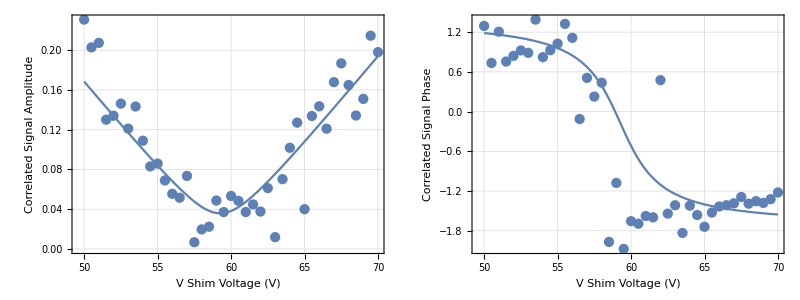
Optimal Voltage: 59.2651 V
{ | System
# Counts | 3500
DDS Att. (dB) | 22.
Step Size (kHz) | 100.
397nm Freq. (MHz) | 18.
397nm Ampl. (% Ampl.) | 102.}
(-Graphics-)

```mathematica
finalDisplay
```

```mathematica
{
53.38,
52.50
};
{Total[%]/2.,(%[[1]]-%[[2]])/2.}
```

{52.94,0.44}

```mathematica
D
```

D